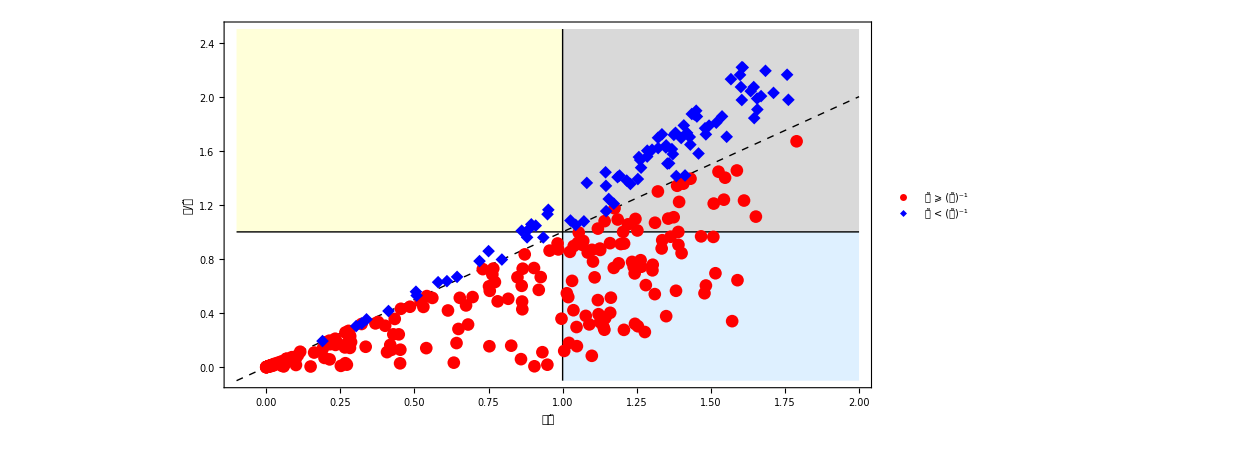

```mathematica
dataDwell=Import["C:\\Users\\Downloads\\ring_hmm_dwell.txt",{"Data",{All},{1,2}}];
dataWait=Import["C:\\Users\\Downloads\\ring_hmm_wait.txt",{"Data",{All},{1,2}}];
plotHMM=ListPlot[{dataDwell, dataWait},Axes->False,GridLines->None,GridLinesStyle->Directive[Thick, Black],Frame->True,BaseStyle->{FontFamily->"Times New Roman",40},FrameStyle->Directive[Black,Thick],AspectRatio->1/2, PlotRange->{{-0.1, 2.0}, {-0.1, 2.5}}, Prolog->{{LightBlue, Rectangle[{1, -0.1}, {2, 1}]},{LightGray, Rectangle[{1, 1}, {2, 2.5}]},{LightYellow, Rectangle[{-0.1, 1}, {1, 2.5}]}, {Dashed,Line[{{-0.1, -0.1}, {2, 2}}]},{Thick,Line[{{1, -0.1}, {1, 2.5}}]}, {Thick,Line[{{-0.1, 1}, {2, 1}}]} }, FrameLabel->{"𝒮𝒯̃","𝒮/𝒜̃"},BaseStyle->{FontFamily->"Times New Roman",40}, PlotLegends->Placed[{Style["𝒯̃ ⩾ (𝒜̃)^-1",FontFamily->"Times New Roman",40], Style["𝒯̃ < (𝒜̃)^-1",FontFamily->"Times New Roman",40]},{0.15,0.75}], PlotMarkers->{{"●",Medium }, {"◆", Medium}}, PlotStyle->{Red, Blue}]
```